Calculation  of  the  Lyapunov  exponent  for  the  Logistic  Map  at  r = 4 
 using  the  analytically  derived  natural  densitiy.

```mathematica
f[x_]:=4x(1-x)
```

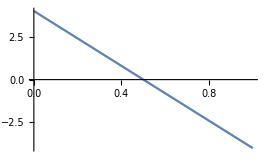

```mathematica
df[x_]:=f'[x]
Plot[df[x],{x,0,1}]
```

```mathematica
rho[x_]:=1/(Pi*Sqrt[x(1-x)])
```

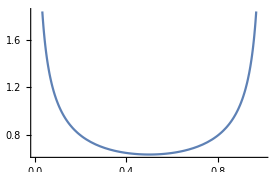

```mathematica
Plot[rho[x],{x,0,1}]
```

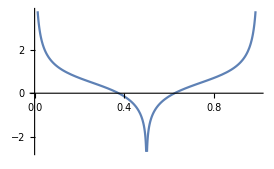

```mathematica
integrand[x_]:=Log[Abs[df[x]]]*rho[x]
Plot[integrand[x],{x,0,1}]
```

```mathematica
Integrate[integrand[x],{x,0,1}]
```

```mathematica
Log[2]
```